```mathematica
F[ydot_,y1_,y2_,y3_,k_]:={ydot-y2+y3,y2+k y3-1,y2 y3-y1/4}
```

```mathematica
MatrixForm[F[ydot,y1,y2,y3,k]]
```

(-y2+y3+ydot
-1+y2+k y3
-y1/4+y2 y3)

```mathematica
Jac=D[F[ydot,y1,y2,y3,k],{{ydot,y2,y3}}]
```

{{1,-1,1},{0,1,k},{0,y3,y2}}

```mathematica
MatrixForm[Jac]
```

(1 | -1 | 1
0 | 1 | k
0 | y3 | y2)

```mathematica
DetJac=Det[Jac]
```

y2-k y3

```mathematica
Sol1=Solve[{F[ydot,Subscript[y1, t0],y2,y3,k]==0},{ydot,y2,y3}]
```

{{ydot→1/2 (1-1/k-√(1-k y1_t0)-(√(1-k y1_t0))/k),y2→1/2 (1-√(1-k y1_t0)),y3→(1+√(1-k y1_t0))/(2 k)},{ydot→1/2-1/(2 k)+1/2 √(1-k y1_t0)+(√(1-k y1_t0))/(2 k),y2→1/2+1/2 √(1-k y1_t0),y3→(1-√(1-k y1_t0))/(2 k)}}

```mathematica
Sol1/.k->-1/.Subscript[y1, t0]->1
```

{{ydot→1,y2→1/2 (1-√2),y3→1/2 (-1-√2)},{ydot→1,y2→1/2+1/(√2),y3→1/2 (-1+√2)}}

```mathematica
DetJacGeneral=DetJac/.Sol1
```

{1/2 (-1-√(1-k y1_t0))+1/2 (1-√(1-k y1_t0)),1/2+1/2 √(1-k y1_t0)+1/2 (-1+√(1-k y1_t0))}

```mathematica
DetJacGeneral/.k->-1/.Subscript[y1, t0]->1
```

{1/2 (-1-√2)+1/2 (1-√2),1/2+1/(√2)+1/2 (-1+√2)}

```mathematica
N[%]
```

{-1.41421,1.41421}

```mathematica
DSolve[
{
y1'[t]==y2[t]+y3[t],
y2[t]- y3[t]-1==0,
y2 [t]y3[t]-y1[t]/4==0,
y1[0]==1,
y1'[0]==1,
y2[0]==1/2 (1-√2),
y3[0]==1/2 (-1-√2)
},
{y1[t],y2[t],y3[t]},t
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

DSolve[{y1'[t]==y2[t]+y3[t],-1+y2[t]-y3[t]==0,-y1[t]/4+y2[t] y3[t]==0,y1[0]==1,y1'[0]==1,y2[0]==1/2 (1-√2),y3[0]==1/2 (-1-√2)},{y1[t],y2[t],y3[t]},t]

```mathematica
Solve[{
y2+k y3-1==0,
y2 y3-y1/4==0
},
{y2,y3}
]
```

{{y2→1/2 (1-√(1-k y1)),y3→(1+√(1-k y1))/(2 k)},{y2→1/2+1/2 √(1-k y1),y3→(1-√(1-k y1))/(2 k)}}

```mathematica
DSolve[
{y1'[t]==(1/2 (1-√(1+ y1[t])))+((1+√(1+ y1[t]))/-2),
y1[0]==1},
y1[t],t
]
```

{{y1[t]→1/4 (4-4 √2 t+t^2)},{y1[t]→1/4 (4+4 √2 t+t^2)}}

```mathematica
Sol2=NDSolve[
{
F[y1'[t],y1[t],y2[t],y3[t],-1][[1]]==0,
F[y1'[t],y1[t],y2[t],y3[t],-1][[2]]==0,
F[y1'[t],y1[t],y2[t],y3[t],-1][[3]]==0,
y1[0]==1
},
{y1[t],y2[t],y3[t]},{t,0,100}]
```

{{y1[t]→InterpolatingFunction[{{0.,100.}},<>][t],y2[t]→InterpolatingFunction[{{0.,100.}},<>][t],y3[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

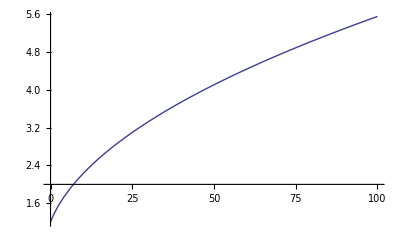

```mathematica
Plot[Evaluate[y2[t]/.Sol2],{t,0,100},PlotRange->All]
```